```mathematica
Integrate[1/Abs[x]*Exp[2*π*I/L*n*x],{x,-L,L}]
```

ConditionalExpression[ExpIntegralEi[-2 ⅈ n π]+ExpIntegralEi[2 ⅈ n π],Re[L]>0&&Im[L]==0]

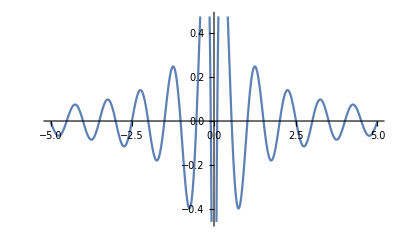

```mathematica
Plot[Re[ExpIntegralEi[-2 ⅈ n π]+ExpIntegralEi[2 ⅈ n π]],{n,-5,5}]
```

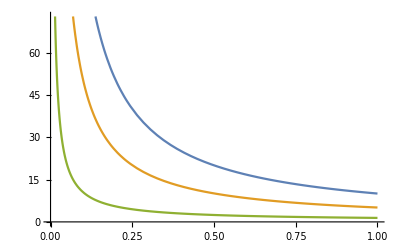

```mathematica
Plot[{10/x*√(1+x/100),5/x*√(1+x/25),1/x*√(1+x)},{x,0,1}]
```

```mathematica
Table[{n,14.2*n/k*√(1+J1/7.1*k/n^2)},{n,1,5}]//TableForm
```

1 | (14.2 √(1+0.140845 J1 k))/k
2 | (28.4 √(1+0.0352113 J1 k))/k
3 | (42.6 √(1+0.0156495 J1 k))/k
4 | (56.8 √(1+0.00880282 J1 k))/k
5 | (71. √(1+0.0056338 J1 k))/k

```mathematica
Manipulate[Plot[14.2*n/k*√(1+J1/(7.1/6.28^2)*k/n^2)*27.211/6.28^2,{k,1,20}],{n,1,5},{J1,0.0,5.0}]
```

```mathematica
Manipulate[Plot[{14.2*1/k*√(1+J1/(7.1)*k/1^2)*27.211/6.28^2,
14.2*2/k*√(1+J1/(7.1)*k/2^2)*27.211/6.28^2,
14.2*3/k*√(1+J1/(7.1)*k/3^2)*27.211/6.28^2,
14.2*4/k*√(1+J1/(7.1)*k/4^2)*27.211/6.28^2},{k,1,100}],
{J1,1.0,5.0}]
```

```mathematica
ϵ0=1.668;
(* N is the number of monomer units *)
(* n is the index of the excited state *)
(* J1 is the interaction strength of the Coulomb potential *)
Manipulate[Plot[Table[2*ϵ0/N*n*√(1+j1/ϵ0*N/n^2),{n,1,10}],{N,1,20}],{j1,0.1,10.0}]
```